```mathematica
121+542
```

663

```mathematica
(-23)76
```

-1748

```mathematica
27^(1/2)
```

3 √3

```mathematica
N[27^(1/2)]
```

5.19615

```mathematica
N[E,50]
```

2.7182818284590452353602874713526624977572470937

```mathematica
N[E^(-5)]
```

0.00673795

```mathematica
Log[Exp[3]]
```

3

```mathematica
Exp[Log[Pi]]
```

π

```mathematica
Abs[-5]
```

5

```mathematica
Cos[Pi/12]
```

(1+√3)/(2 √2)

```mathematica
N[Cos[Pi/12]]
```

0.965926

```mathematica
N[Tan[1000]]
```

1.47032

```mathematica
Cos[x]^2+Sin[x]^2
```

Cos[x]^2+Sin[x]^2

```mathematica
Simplify[Cos[x]^2+Sin[x]^2]
```

1

```mathematica
TrigExpand[Cos[3x]]
```

Cos[x]^3-3 Cos[x] Sin[x]^2

```mathematica
TrigReduce[Sin[3x]Cos[4x]]
```

1/2 (-Sin[x]+Sin[7 x])

```mathematica
Factor[12x^2+27x y-84y^2]
```

3 (4 x-7 y) (x+4 y)

```mathematica
Expand[(x+y)^2(3x-y)^3]
```

27 x^5+27 x^4 y-18 x^3 y^2-10 x^2 y^3+7 x y^4-y^5

```mathematica
Together[2/(x^2)-x^2/2]
```

(4-x^4)/(2 x^2)

```mathematica
Apart[1/((x-3)(x-1))]
```

1/(2 (-3+x))-1/(2 (-1+x))

```mathematica
Cancel[(x^2-1)/(x^2-2x+1)]
```

(1+x)/(-1+x)

```mathematica
Simplify[(2(x-3)^2(x+1))/(3(x+1)^(4/3))+2(x-3)(x+1)^(2/3)]
```

(8 (-3+x) x)/(3 (1+x)^(1/3))

```mathematica
x = dog
```

dog

dog

```mathematica
Dynamic[x]
```

```mathematica
x=7
Dynamic[x]
```

7

```mathematica
Clear[x];
f[x_] = (x^2+2x)/(6x);
f[x]/.x-> 7
```

3/2

```mathematica
f[x_]= x/(x^2+1)
f[3]
f[a]
```

x/(1+x^2)

3/10

a/(1+a^2)

```mathematica
Simplify[(f[3+h]-f[3])/h]/.h->0
```

-2/25

```mathematica
list={1,2,3,4,5};
f[x_]=x^2;
Map[f,list]
```

{1,4,9,16,25}

```mathematica
h[t_]=(1+t)^(1/t);
Limit[h[t], t-> 0]
```

ⅇ

```mathematica
Clear[f]
f[0]=1;
f[1]=1;
f[n_]:=f[n-1]+f[n-2];
Table[f[n],{n,0,10}]
```

{1,1,2,3,5,8,13,21,34,55,89}

```mathematica
Clear[f];
f[t_]:=Sin[1/t]/;t>0;
f[t_]:=-t/;t≤0;
f[1/(10Pi)]
f[-5]
```

0

5

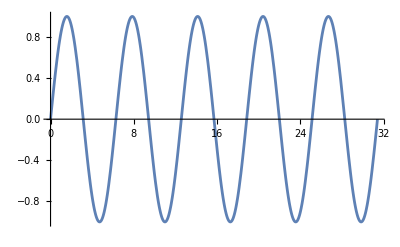

```mathematica
Plot[Sin[x],{x,0,10Pi}]
```

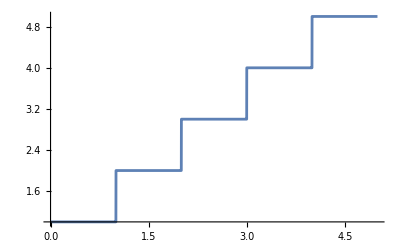

```mathematica
s[t_]:=1/;0≤t<1;
s[t_]:=1+s[t-1]/;t≥1;
Plot[s[t],{t,0,5}]
```

```mathematica
f[x_]=Exp[x];
g[x_]=Log[x];
f[g[x]]
Simplify[f[g[x]]]
```

x

x

```mathematica
Solve[3x+4==7,x]
```

{{x→1}}

```mathematica
Solve[x^3+x^2+x+1==0,x]
```

{{x→-1},{x→-ⅈ},{x→ⅈ}}

```mathematica
Solve[a^2+b^2==c^2,a]
```

{{a→-√(-b^2+c^2)},{a→√(-b^2+c^2)}}

```mathematica
Solve[Sin[x]^2-2Sin[x]-3==0,x]
```

{{x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(3 π)/2+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π-ArcSin[3]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcSin[3]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Clear[f];
f[x_]=Sin[2x]+2Cos[x];
Solve[f'[x]==0,x]
```

{{x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π/6+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(5 π)/6+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[{3x-y==4,x+y==2},{x,y}]
```

{{x→3/2,y→1/2}}

```mathematica
Solve[{x^2/a^2+y^2/b^2==1,y==m x},{x,y}]
```

{{x→-(a b)/(√(b^2+a^2 m^2)),y→-(a b m)/(√(b^2+a^2 m^2))},{x→(a b)/(√(b^2+a^2 m^2)),y→(a b m)/(√(b^2+a^2 m^2))}}

```mathematica
N[Solve[x^4-2x^2==1-x]]
```

{{x→-1.71064},{x→1.34509},{x→0.182777-0.633397 ⅈ},{x→0.182777+0.633397 ⅈ}}

```mathematica
Solve[x==Tan[x]]
FindRoot[x==Tan[x],{x,4}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[x==Tan[x]]

{x→4.49341}

```mathematica
NSolve[{x^2+4x y+y^2==4,5x^2-4x y +2y^2==8}]
```

{{x→-1.39262,y→-0.348155},{x→1.39262,y→0.348155},{x→0.,y→2.},{x→0.,y→-2.}}

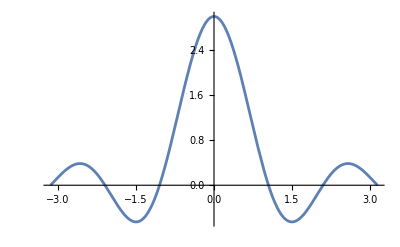

3

```mathematica
Clear[f];
f[x_]:= Sin[3x]/x;
Plot[f[x],{x,-Pi,Pi}]
Limit[f[x],x -> 0]
```

```mathematica
Limit[(2x^2+25x+72)/(72-47x-14x^2),x -> -9/2]
```

7/79

```mathematica
Limit[1/Log[x]-1/(x-1),x -> 1,Direction->1]
```

```mathematica
1/2
```

1/2

```mathematica
Limit[(1+z/x)^x,x -> Infinity]
```

ⅇ^z

```mathematica
Clear[f];
f[x_]=Sin[2x];
Limit[(f[x+h]-f[x])/h,h -> 0]
D[f[x],x]
f'[x]
D[f[x],{x,2}]
f''[x]
```

2 Cos[2 x]

2 Cos[2 x]

2 Cos[2 x]

-4 Sin[2 x]

-4 Sin[2 x]

```mathematica
Clear[f,g];
Together[D[f[x]/g[x],x]]
D[f[x]g[x],x]
```

(g[x] f'[x]-f[x] g'[x])/g[x]^2

g[x] f'[x]+f[x] g'[x]

```mathematica
D[ArcSin[x],x]
```

1/(√(1-x^2))

```mathematica
f[x_]=Cos[Exp[x*y[x]]]-x;
Solve[D[f[x],x]==0,y'[x]]
Solve[Dt[f[x]]==0,y'[x]]
```

{{y'[x]→-(ⅇ^(-x y[x]) (Csc[ⅇ^(x y[x])]+ⅇ^(x y[x]) y[x]))/x}}

{{y'[x]→-(ⅇ^(-x y[x]) (Csc[ⅇ^(x y[x])]+ⅇ^(x y[x]) y[x]))/x}}

```mathematica
Clear[f]
f[x_]:= x^2-3x;
Solve[f'[c]==(f[7/2]-f[0])/(7/2-0),c]
```

{{c→7/4}}

```mathematica
f[x_]:=x^2Sin[1/x]^2;/Assumptions->x!=0;
f[0]:= 0
Limit[(f[0+h]-f[0])/h,h->0]
```

0

```mathematica
Maximize[x/(x^2+1),x]
```

{1/2,{x→1}}

```mathematica
Minimize[x/(x^2+1),x]
```

{-1/2,{x→-1}}

```mathematica
Integrate[Exp[1/x]/x^2,x]
∫Exp[1/x]/x^2 ⅆx
```

-ⅇ^(1/x)

-ⅇ^(1/x)

```mathematica
Integrate[Sin[x]/x,x]
```

SinIntegral[x]

```mathematica
Integrate[(x^2+1)/Sqrt[x],{x,1,4}]
```

72/5

```mathematica
Integrate[Exp[-x^2],{x,-Infinity,Infinity}]
Integrate[1/(Sqrt[k^2-x^2]),{x,0,k}]
```

√π

ConditionalExpression[π/2, Re[k]>0&&Im[k]==0]

```mathematica
Integrate[Abs[Sin[x]-Cos[x]],{x,0,2Pi}]
```

4 √2

```mathematica
Clear[f];
f[x_]=x^4/8+1/(4x^2);
Integrate[Sqrt[1+f'[x]^2],{x,1,2}]
```

33/16

```mathematica
c[n_]:= Integrate[(1-x^2)^n,{x,-1,1}]^{-1};
Table[c[n],{n,1,10}]
Limit[c[n],n -> Infinity]
Integrate[c[n](1-x^2)^n,{x,-1,1}]-1
```

{{3/4},{15/16},{35/32},{315/256},{693/512},{3003/2048},{6435/4096},{109395/65536},{230945/131072},{969969/524288}}

{∞}

{ConditionalExpression[0, Re[n]>-1]}

```mathematica
DSolve[D[w[x],x]== -Sqrt[2w[x]^3+c*w[x]^2],w[x],x]//Simplify
```

{{w[x]→-1/2 c Sech[1/2 √c (x-C[1])]^2}}

```mathematica
L={{p,q},{q,-p}};
L//MatrixForm
A = {{0,-1/2},{1/2,0}};
eqns = {D[L[t],t]==A.L-L.A}
L.L//MatrixForm
```

(p | q
q | -p)

{{{0,0},{0,0}}[t]+{{p,q},{q,-p}}'[t]=={{-q,p},{p,q}}}

(p^2+q^2 | 0
0 | p^2+q^2)

```mathematica
DSolve[D[u[x,t],{x,2}]== D[u[x,t],{t,2}],u,{x,t}]
```

```mathematica
A= {{a,b},{c,d}};
J={{1,0},{0,1}};
f[x_]:=Det[x*J-A];
a[n_]=Coefficient[f[q],q^n];
Sum[a[n]A^n,{n,0,2}]
```

{{0,0},{0,0}}

```mathematica
Solve[{x^2-x*y+y^2-21==0,y^2-2x*y+15==0},{x,y}]
```

{{x→-4,y→-5},{x→4,y→5},{x→-3 √3,y→-√3},{x→3 √3,y→√3}}